```mathematica
Clear[QCTMC];
QCTMC=QueueInit[4,2,"A"];
GovME=GovernMat[QCTMC];
GovM=N[GovME];
t= Power[2,0];
```

```mathematica
exact=MatrixExp[GovME*t];
```

$Aborted

```mathematica
(*Pade*)
TimeListPade=List[];
ErrorListPade=List[];
Do[
Res=AbsoluteTiming[Pade[GovM*t,i]];
time=Res[[1]];
ExactError=Max[Abs[Res[[2]]-exact]];
AppendTo[ErrorListPade,ExactError];
AppendTo[TimeListPade,time];
,{i,20}]
```

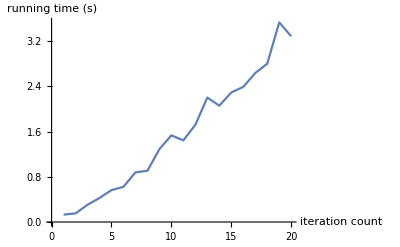

```mathematica
TimeListPadePlot=ListLinePlot[TimeListPade,AxesLabel->{"iteration count","running time (s)"}]
Export["4_4_InitSortAcu.eps",First@ImportString[ExportString[TimeListPadePlot,"PDF"]]];
```

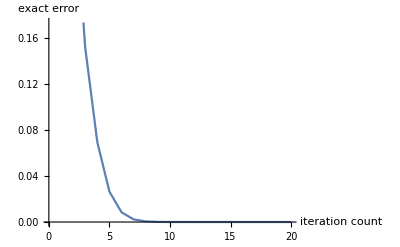

```mathematica
ListLinePlot[ErrorListPade,AxesLabel->{"iteration count","exact error"}]
```

```mathematica
ErrorListPade
```

{0.666712,0.30228,0.151558,0.0692847,0.0263933,0.00843959,0.00228267,0.000526276,0.000104217,0.0000178572,2.66623×10^-6,3.49203×10^-7,4.03715×10^-8,4.1439×10^-9,3.79663×10^-10,3.13054×10^-11,2.64233×10^-12,3.37397×10^-13,4.19109×10^-13,1.34559×10^-13}

```mathematica
TimeListPade
```

{0.0109478,0.00471764,0.0403118,0.00537387,0.0068302,0.00868546,0.0107771,0.0126628,0.0149133,0.0500455,0.0177383,0.0191033,0.0224509,0.0257136,0.0268285,0.0284329,0.0303027,0.032929,0.0356515,0.0375497}

```mathematica
(*scaling and squaring*)
TimeListSS=List[];
ErrorListSS=List[];
Ti=1;
Do[
Res=AbsoluteTiming[SS[GovM*t,i]];
time=Res[[1]];
ExactError=Max[Abs[Res[[2]][[1]]-exact]];
AppendTo[ErrorListSS,ExactError];
AppendTo[TimeListSS,time];
,{i,20}]
```

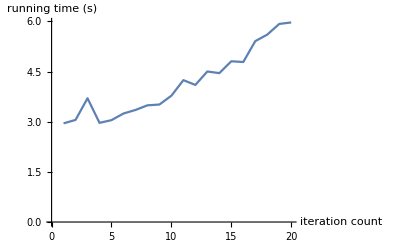

```mathematica
ListLinePlot[TimeListSS,AxesLabel->{"iteration count","running time (s)"}]
```

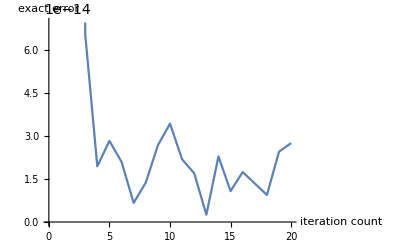

```mathematica
ListLinePlot[ErrorListSS,AxesLabel->{"iteration count","exact error"}]
```

```mathematica
(*Krylov Subspace*)
```

```mathematica
t=1024
```

1024

```mathematica
v0=L2V[QCTMC,RandomInitState[QCTMC]];
```

```mathematica
Dimensions[v0]
```

{1024,1}

```mathematica
ExactV=MatrixExp[GovM*t,Flatten[v0]];
```

```mathematica
KryRes=MatrixExp[GovM*t,Flatten[v0],Method->"Krylov"];
```

```mathematica
KryParaTimeList=List[];
KryParaErrorList=List[];
KryParaErrorList2=List[];
TempList=List[];
Do[
KryParaRes=AbsoluteTiming[MatrixExponentialKrylov[GovM*t,v0,i,1]];
AppendTo[KryParaTimeList,KryParaRes[[1]]];
ExactError=Max[Abs[KryParaRes[[2]]-ExactV]];
AppendTo[KryParaErrorList,ExactError];
AppendTo[TempList,Max[Abs[ExactV-KryRes]]];
Print[i];
,{i,1,80}]
```

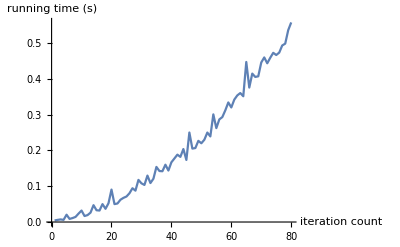

```mathematica
KryIterTime=ListLinePlot[KryParaTimeList,AxesLabel->{"iteration count","running time (s)"}]
```

```mathematica
Export["C:\\Users\\mei\\Desktop\\Numerical methods\\EPS_figure\\KryIterTime.eps",KryIterTime]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\KryIterTime.eps

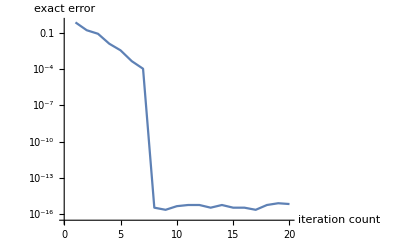

```mathematica
KryIterError=ListLinePlot[KryParaErrorList[[1;;20]],AxesLabel->{"iteration count","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export["C:\\Users\\mei\\Desktop\\Numerical methods\\EPS_figure\\KryIterError.eps",KryIterError]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\KryIterError.eps

```mathematica
KryParaErrorList
```

{0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,6.69326×10^-14,9.66033×10^-14,3.00593×10^-14,3.37508×10^-14,2.54657×10^-14,5.69128×10^-14,3.07393×10^-14,3.93574×10^-14,4.97102×10^-14,2.30137×10^-14,2.5438×10^-14}

```mathematica
KryParaErrorList[[1;;11]]
```

{0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,0.121584,6.69326×10^-14,9.66033×10^-14}

```mathematica
KryParaRes=AbsoluteTiming[MatrixExponentialKrylov[GovM*t,v0,16,1]];
```

{{-0.981744,0.999833,0.585952,0.167577,-0.610548,-0.0065379,0.0615386,0.000232255,-0.30965,0,0,0,0,0,0,0},{0.999833,-1.01826,-0.596749,-0.170665,0.621798,0.00665837,-0.0626726,-0.000236534,0.315356,0,0,0,0,0,0,0},{0,2.05096×10^-16,-0.151214,0.528737,-0.358966,-0.0038439,0.365171,0.0013782,0.0562082,0,0,0,0,0,0,0},{0,0,0.528737,-1.84879,1.25516,0.0134406,-1.27686,-0.00481904,-0.196538,0,0,0,0,0,0,0},{0,0,0,8.30931×10^-16,-0.000229307,0.0214141,-0.000250841,-9.46709×10^-7,-0.000661259,0,0,0,0,0,0,0},{0,0,0,0,0.0214141,-1.99977,0.0234251,0.0000884093,0.0617523,0,0,0,0,0,0,0},{0,0,0,0,0,2.02637×10^-14,-0.0000284877,0.00754816,-0.000049664,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.00754816,-1.99997,0.0131591,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,4.90451×10^-14,-2.84262×10^-16,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,7.3685×10^-17,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
res=KryParaRes[[2]]
```

{0.216441,-0.161192,0.,0.,-0.161192,0.232225,0.,0.,0.,0.,0.0482641,0.0000633907,0.,0.,0.0000633907,0.50307}

```mathematica
MatrixExp[GovM*t,Flatten[v0]]-res
```

{-1.38778×10^-16,5.55112×10^-17,0.,0.,8.32667×10^-17,-1.66533×10^-16,0.,0.,0.,0.,-4.85723×10^-17,-1.5748×10^-17,0.,0.,1.99222×10^-18,-2.22045×10^-16}

```mathematica
KryParaErrorList
```

{0.302151,5.72542×10^-13,1.19793×10^-13,1.16462×10^-13,8.27671×10^-14,1.16462×10^-13,8.58758×10^-14,1.16462×10^-13,1.87961×10^-13,9.26481×10^-14,6.41709×10^-14,1.23512×10^-13,1.25011×10^-13,1.23512×10^-13,1.17573×10^-13,1.23512×10^-13,6.43374×10^-14,1.23512×10^-13,3.7248×10^-14,1.23512×10^-13,9.27036×10^-14,1.23512×10^-13,3.07254×10^-14,8.69305×10^-14,5.83422×10^-14,8.69305×10^-14,1.0808×10^-13,8.69305×10^-14,3.29736×10^-14,8.69305×10^-14,1.72973×10^-13,1.36002×10^-13,3.90799×10^-14,9.4702×10^-14,4.30767×10^-14,7.47735×10^-14,4.17444×10^-14,2.12275×10^-13,4.26326×10^-14,4.51861×10^-14,1.32894×10^-13,1.54043×10^-13,7.28861×10^-14,2.15827×10^-13,6.41154×10^-14,7.17204×10^-14,1.60372×10^-13,1.48548×10^-13,1.59428×10^-13,1.59484×10^-13,4.41314×10^-14,1.2812×10^-13,8.32112×10^-14,1.63036×10^-13,4.06342×10^-14,1.0858×10^-13,1.63702×10^-13,1.54099×10^-13,9.03166×10^-14,1.04416×10^-13,1.249×10^-13,1.04694×10^-13,1.36779×10^-13,1.02751×10^-13}